## I)SIR with B(s,i)=β s /(1+μ i) and T(i)=η w i/(i+w) preliminaries

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
Params={Λ,δ,γ,β,ξ,ω,μ,α};
cet0={η->0};

Lgn=(γ+Λ+δ); cir={ir->γ-is};
sd=Λ/μ;R1=β/Subscript[V, 2];R0=sd R1 (*basic reproduction number*);η0=sd β-Subscript[v, 2] ;ωH=(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ));
Print["R0  =",R0," ,η0=",η0 ," ,ωH=",ωH," and critical β is ", b0=β/.Solve[R0==1,β][[1]]//FullSimplify]
(*Conditions de positivité*)
cp={Λ>0,δ>0,γ>0,β>0,ξ>0,μ/Subscript[v, 1]>ω>0,η>0,μ>0,α>0,Subscript[v, 1]>0,Subscript[v, 2]>0};
<<"def.m";(*Contains icd,tre,tre11,tre12,tre2,trR,trE2*)
(*Print["Bautin"]
Timing[trz=FullSimplify[Reduce[Join[{trR==0(*&&dis==0*)},cp]]]]*)
(*Numerical conditions used in first tests*)
Param=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{16,2/10,12/100,1/100,1/1000,12/100,μ+γ+δ,β+ μ ξ,μ+γ+δ+η}];
ParamF=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{16,2/10,12/100,1/100,1/1000,1/10,μ+γ+δ,β+ μ ξ,μ+γ+δ+η}];
paramGc=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{1/2,2/10,1/10,2/10,7/100,1/10,(μ+γ+δ),(β+ μ ξ),μ+γ+δ+η}];(*Parameters of Figure 4 in Zhou Fan*)
ParNumCheck=Thread[{ω,α,η}->{7/64,179/64,α/ω}];
Print["test cNN="]
cNN=Join[ParNumCheck,Param]


(*conditions for switching between the parameters and particular cases*)
cv2={Subscript[v, 2]->(μ+γ+δ)};cv1={Subscript[v, 1]->(β+ μ ξ)};cV2={Subscript[V, 2]->(Subscript[v, 2]+η)};
cv={ξ ->(Subscript[v, 1]-β)/μ,δ ->Subscript[v, 2]-(μ+γ),η->Subscript[V, 2]-Subscript[v, 2]};ceta={η->α/ω};calv1={α-> ω (Subscript[v, 1]-β)/μ};
```

R0  =(β Λ)/(μ V_2) ,η0=(β Λ)/μ-v_2 ,ωH=(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ)) and critical β is (μ V_2)/Λ

test cNN=

{ω→7/64,α→179/64,η→α/ω,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ}

### 0) Model, eqF, sol, Jacobian, jacE0, equation for endemic i, Discriminant, ie ,se2,trE2,detE2

( s'
i'
r')= (Λ-s μ-(i s β)/(1+i ξ)
-i (γ+δ+μ)+(i s β)/(1+i ξ)-(i η ω)/(i+ω)
i γ-r μ+(i η ω)/(i+ω))

simulation test

{133.333,4.9801×10^-27,-8.73471×10^-13}

For 2-dim case, ωe have ( s'
i')=(Λ-s μ-(i s β)/(1+i ξ)
-i (γ+δ+μ)+(i s β)/(1+i ξ)-(i η ω)/(i+ω))

numeric equil are

{{s→133.333,i→0.},{s→86.1361,i→6.61878},{s→69.9589,i→10.99}}

2 dim jac=(-μ-(i β)/(1+i ξ) | -(s β)/(1+i ξ)^2
(i β)/(1+i ξ) | -γ-δ-μ+(s β)/(1+i ξ)^2-(η ω^2)/(i+ω)^2)

jac(DFE)=(-μ | -(β Λ)/μ
0 | (β Λ-μ (γ+δ+η+μ))/μ)

trF= -γ-δ-2 μ-(β (i-s+i^2 ξ))/(1+i ξ)^2-(η ω^2)/(i+ω)^2

Det(J(E0)=-β Λ+μ (γ+δ+η+μ), and Tr(J(E0))=-γ-δ-η+(β Λ)/μ-2 μ

simple det formula: detF=μ^2-(s β μ)/(1+i ξ)^2+(i β μ)/(1+i ξ)+γ (μ+(i β)/(1+i ξ))+δ (μ+(i β)/(1+i ξ))+(η μ ω^2)/(i+ω)^2+(i β η ω^2)/((1+i ξ) (i+ω)^2)

s formula cs is

{s→(Λ (1+i ξ))/(i β+μ+i μ ξ)}

sec. order A i^2 + B i + C=0 for endemic i is

-β Λ ω+i^2 v_1 v_2+μ ω V_2+i (-β Λ+μ v_2+ω v_1 V_2)

check  poli/poliF=

1

coeffs are

{A,B,C} ={(γ+δ+μ) (β+μ ξ),-β Λ+μ (γ+δ+μ)+(γ+δ+η+μ) (β+μ ξ) ω,(-β Λ+μ (γ+δ+η+μ)) ω}

i1,  icd, i2

{6.61878,7.61514,10.99}

H  has coords

{(β Λ)/μ-v_2,(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ))}

and trH=

{0.0625,-μ}

The discriminant Δ = B^2 - 4 A C= μ^2 (γ+δ+μ-(γ+δ+η+μ) ξ ω)^2+β^2 (Λ^2+2 Λ (γ+δ-η+μ) ω+(γ+δ+η+μ)^2 ω^2)+2 β μ (-Λ (γ+δ+μ)-(γ+δ+μ) (γ+δ+η+μ) ω+Λ (γ+δ-η+μ) ξ ω+(γ+δ+η+μ)^2 ξ ω^2) at H it is

0

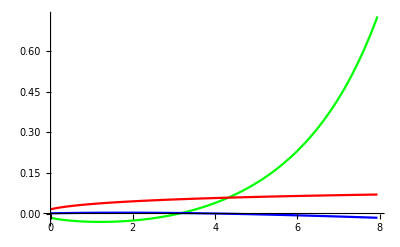

```mathematica
(*SIR  epidemic model of Fan:*) 
s1=Λ -   β s  i/(1+ξ i)-s μ ;(*λ s (1-s/K)*)
i1= β s   i/(1+ξ i)-Subscript[v, 2] i -η ω i/(i+ω);
r1=η  ω i/(i+ω)-μ r + γ i ;

dyn={s1,i1,r1}//.cv2;(*field*)
vars={s,i,r};
equi=Solve[Thread[dyn==0],vars];

 Print["( s'
i'
r')= ",dyn//MatrixForm]
 
(*Diff. sys and Numerical test:*)
varst=Through[vars[t]];(*Map[#[t]&, vars];Revarst = Thread[vars->varst]*);
diff= D[varst,t] − (dyn/.Thread[vars->varst]);
diffN=diff//.cNN;
initcond = (varst/.t->0)-{1.5, 0.5, 0.1};
eqs=Thread[Flatten[{diffN, initcond}] == 0];
ndesoln = NDSolveValue[eqs,varst,{t, 0, 1000}];
Print["simulation test"]
ndesoln/.t->1000

(*Two dimensional Fan:*)
dyn2={s1,i1}/.cv2;(*ωe may reduce to this dyntem since these tωo equations
 do not depend on r*)
 Print["For 2-dim case, ωe have ( s'
i')=",dyn2//MatrixForm]
 eqF=Thread[Flatten[dyn2==0]];
 equi2=Solve[eqF,{s,i}];
 Print[" numeric equil are"]
equi2//.cNN//N
 dyn2E={s1,Simplify[i1/i]}/.cv2;
 
(*Computation of the Jacobian  *)

jac=Grad[dyn2,{s,i}]//FullSimplify;
det=Det[jac]//FullSimplify;
Print["2 dim jac=",jac//MatrixForm]
jacE0=(jac/.i->0/.s->sd)//FullSimplify;
Print["jac(DFE)=", jacE0//MatrixForm]
tr=Tr[jac]//FullSimplify;
Print["trF= ",tr]
detE0=Det[jacE0]//FullSimplify;trE0=Tr[jacE0]//FullSimplify;

Print["Det(J(E0)=",detE0, ", and Tr(J(E0))=", Apart[trE0]]

(*Elimination of s via plugging, for trace and det*)
Print["simple det formula: detF=",det]
Print["s formula cs is"]
cs=Flatten[Solve[dyn2[[1]]==0,s]]


(*Equation for endemic i *)
poli=Collect[Factor[Numerator[Together[dyn[[2]]/.cs]]]/(-i),i];
Print["sec. order A i^2 + B i + C=0 for endemic i is"]
polv= Collect[ poli/.cv//FullSimplify,i]
(*Mathematica Eliminate*)
el=Eliminate[eqF,{s}]//FullSimplify;
poliF=Collect[Numerator[Factor[el[[1,1]]-el[[1,2]]]/(-i)]//FullSimplify,i];
Print["check  poli/poliF="]
poli/poliF//FullSimplify

Print["coeffs are"]
cf=CoefficientList[poli,i];
Aa=cf[[3]];Bb=cf[[2]]; Cc=cf[[1]];
Print["{A,B,C} =",{Aa,Bb,Cc}//FullSimplify//.cv2]

ie=i/.Solve[poli==0,i];

ic0=(-Bb/(2 Aa));
se1=Λ ( 1+ξ ie[[1]])/(μ+ ie[[1]] Subscript[v, 1])(*endemic s*);
se2=Λ ( 1+ξ ie[[2]])/(μ+ ie[[2]] Subscript[v, 1]);
se0=Λ ( 1+ξ ic0)/(μ+ ic0 Subscript[v, 1]);

detE2=det/.s->se2/.i->ie[[2]];
detE1=det/.s->se1/.i->ie[[1]];
detE=det/.s->se0 /.i->ic0(* det ωhen $i=-B/(2A)**);

trE2=tr/.i->ie[[2]]/.s->se2;
trE1=tr/.i->ie[[1]]/.s->se1;

(*Print["Det i"]
deti=Simplify[(detF/.cs)( 1+ξ i)(( ω + i)^2)( μ+(μ ξ+β) i)]/.cv//FullSimplify
Print["PolynomialRemainder detR"]
detR=PolynomialRemainder[deti,poli,i];
Timing[icd=i/.Solve[detR==0,i][[1]]//FullSimplify]*)
Print["i1,  icd, i2"] 
Chop[{ie[[1]],icd,ie[[2]]}//.cNN//N]

dis=Discriminant[poli,i]//FullSimplify;
Save["def.m",dis]
(*ωH=ω/.Flatten[Solve[(Bb/.η->η0)==0,ω]/.cv2//FullSimplify]*)
Print[" H  has coords "]
{η0,ωH}
Print["  and trH="]
Timing[trH=trE2/.{η->η0,ω->ωH}//.cv2//FullSimplify]
Print["The discriminant Δ = B^2 - 4 A C= ",dis," at H it is"]
(dis/.{η->η0,ω->ωH})//.cv2//FullSimplify

p1=Plot[{detE1}//.Drop[cNN,{1}]//N,{ω,0,ωH}//.Drop[cNN,{1}]//N,PlotStyle->{Green}];
p0=Plot[{detE}//.Drop[cNN,{1}]//N,{ω,0,ωH}//.Drop[cNN,{1}]//N,PlotStyle->{Blue}];
(*p0n=Plot[{detEn}//.Drop[cNN,{1}]//N,{ω,0,ωH}//.Drop[cNN,{1}]//N,PlotStyle->{Yellow}];*)
p2=Plot[{detE2}//.Drop[cNN,{1}]//N,{ω,0,ωH}//.Drop[cNN,{1}]//N,PlotStyle->{Red}];
cs2=Flatten[Solve[(dyn2[[2]]/i)==0,s]];
se02=s/.cs2;
detEn=det/.s->se02 /.i->ic0;
p102=Show[p1,p0,p2,PlotRange->All,AxesOrigin->{0,0}]
(*Export["p102.pdf",p102]*)
```

```mathematica
RI=FindInstance[Join[{dis>0,R0<1,(trE2)>0, Bb<0},cp,{η==α/ω}]//.Param,{ω,α,η}];
RVI=FindInstance[Join[{dis>0,R0<1,(trE2)<0},cp,{η==α/ω}]//.Param,{ω,α,η}];
RII=FindInstance[Join[{dis>0,R0>1,(trE2)>0},cp,{η==α/ω}]//.Param,{ω,α,η}];
RIII=FindInstance[Join[{dis>0,R0>1,(trE2)<0},cp,{η==α/ω}]//.Param,{ω,α,η}];
RIV=FindInstance[Join[{dis>0&&R0<1&&Bb>0},cp,{η==α/ω}]//.Param,{ω,α,η}];
RV=FindInstance[Join[{dis<0,R0<1},cp,{η==α/ω}]//.Param,{ω,α,η}];
BoIIandIII=FindInstance[Join[{dis>0&&trE2==0 &&Bb<0&&R0>1},cp,{η==α/ω}]//.Param,{ω,α,η}];
BoIIandI=FindInstance[Join[{dis>0&&trE2>0 &&Bb<0&&R0==1},cp,{η==α/ω}]//.Param,{ω,α,η}];
BoIIandIV=FindInstance[Join[{dis>0 &&Bb>0&&R0==1},cp,{η==α/ω}]//.Param,{ω,α,η}];
BoIandVI=FindInstance[Join[{dis>0 &&Bb<0&&trE2==0&&R0<1},cp,{η==α/ω}]//.Param,{ω,α,η}];

Print["HP"]
HP=NSolve[Join[{η==η0&&Bb==0},cp,{η==α/ω}]//.Param,{ω,α,η}]
Print["BTP"]
eq=Flatten[Join[{dis==0&&trE2==0},cp,{α==η ω}]]//.Param;
BTP=Solve[eq,{ω,α,η},Reals]
BTP//N

Print["BP"]
BP=Solve[Join[{η==η0&&trE2==0&&dis>0},cp,{η==α/ω}]//.Param,{ω,α,η},Reals]
BP//N



ParRI=Thread[{ω,α}->({ω,α}//.RI[[1]])];
ParRVI=Thread[{ω,α}->({ω,α}//.RVI[[1]])];
ParRII=Thread[{ω,α}->({ω,α}//.RII[[1]])];
ParRIII=Thread[{ω,α}->({ω,α}//.RIII[[1]])];
ParRIV=Thread[{ω,α}->({ω,α}//.RIV[[1]])];
ParRV=Thread[{ω,α}->({ω,α}//.RV[[1]])];
ParHP=Thread[{ω,η}->({ω,η}//.HP[[1]])];
ParBTP=Thread[{ω,α,η}->({ω,α,η}//.BTP[[1]])];
ParBP=Thread[{ω,α,η}->({ω,α,η}//.BP[[1]])];
ParBoIIandIII=Thread[{ω,α}->({ω,α}//.BoIIandIII[[1]])];
ParBoIIandI=Thread[{ω,α}->({ω,α}//.BoIIandI[[1]])];
ParBoIIandIV=Thread[{ω,α}->({ω,α}//.BoIIandIV[[1]])];
ParBoIandVI=Thread[{ω,α}->({ω,α}//.BoIandVI[[1]])];
ParGca=Thread[{ω,α}->{10/99, 9/99}];
ParGcb=Thread[{ω,α}->{10000/103387, 9000/103387}];
ParGcc=Thread[{ω,α}->{10/108, 9/108}];
ParGcd=Thread[{ω,α}->{1/11, 9/110}];
ParGc4=Thread[{ω,α}->{1000000000/1604038240, 900000000/1604038240}];
ParG3a=Thread[{ω,α}->{100000000/1063265757, 90000000/1063265757}];

testGca=Join[paramGc,ParGca];
testGcb=Join[paramGc,ParGcb];
testGcc=Join[paramGc,ParGcc];
testGcd=Join[paramGc,ParGcd];
testGc4=Join[paramGc,ParGc4];
Print["testG3a"]
testG3a=Join[paramGc,ParG3a]
Print["testI"]
test["I"]=Join[Param,ParRI]
test[VI]=Join[Param,ParRVI];
Print["testII"]
test[II]=Join[Param,ParRII]

Print["testIII"]
test[III]=Join[Param,ParRIII]

test[IV]=Join[Param,ParRIV];
test[V]=Join[Param,ParRV];

testBoIIandIII=Join[Param,ParBoIIandIII];
Print["testBoIIandIII"]
testBoIIandIII
testBoIIandIV=Join[Param,ParBoIIandIV];
testBoIIandI=Join[Param,ParBoIIandI];
Print["testBoIIandI"]
testBoIIandI//N
R0//.ceta//.testBoIIandI//N
trE2//.ceta//.testBoIIandI//N

testBoIandVI=Join[Param,ParBoIandVI];testBoIandVI//N;
R0TD={R0-1, trE2, dis, Bb};
Print["R0-1, Tr,Dis, B for region I is "]
R0TD//.Join[test["I"],ceta]//N
Print["R0-1, Tr,Dis, B for the boundary betωeen II and III is "]
Chop[Evaluate[R0TD//.Join[testBoIIandIII,ceta]//N]]
Print["R0-1, Tr,Dis, B of Gupta (Fig 1a) is : "]
R0TD//.Join[testGca,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1b) is : "]
R0TD//.Join[testGcb,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1c) is : "]
R0TD//.Join[testGcc,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1d) is : "]
R0TD//.Join[testGcd,ceta]//N
Print["R0-1, Tr,Dis, B, of Gupta (Fig 3a) is : "]
R0TD//.Join[testG3a,ceta]//N

Print["at H, dis is"]
testHP=Join[Param,ParHP,{η->α/ω}];
testBTP=Join[Param,ParBTP];
testBP=Join[Param,ParBP];
dis//.testHP//FullSimplify

Print["TrE2 at H when μ=1/12 is "]
trE2//.testHP//N
```

HP

{{η→0.893333,ω→7.94466,α→7.09723}}

BTP

{{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→Root0.907Root[{-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,-105964922164454091786561126032135553701906191046490140625000000000000000000000000000000000000000000+3093341524399952828629414823089460458613070926447063484375000000000000000000000000000000000000000 #1+741204785031856789210639778263565055157008677892222104390625000000000000000000000000000000000000 #1^2+130643513428258106317298763332917647206314030488478125000000000000000000000000000000000000000000000 #2-11017602965783100299425529041076054914399149904528321875000000000000000000000000000000000000000000 #1 #2&},{3,1}]0.9066570098251091 Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,η→Root0.907Root[{-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,-105964922164454091786561126032135553701906191046490140625000000000000000000000000000000000000000000+3093341524399952828629414823089460458613070926447063484375000000000000000000000000000000000000000 #1+741204785031856789210639778263565055157008677892222104390625000000000000000000000000000000000000 #1^2+130643513428258106317298763332917647206314030488478125000000000000000000000000000000000000000000000 #2-11017602965783100299425529041076054914399149904528321875000000000000000000000000000000000000000000 #1 #2&},{3,1}]0.9066570098251091}}

{{ω→6.84183,α→6.20319,η→0.906657}}

BP

{{ω→Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656742,α→67/75 Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656742,η→67/75},{ω→Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257576,α→67/75 Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257576,η→67/75}}

{{ω→5.15735,α→4.60724,η→0.893333},{ω→7.35966,α→6.57463,η→0.893333}}

testG3a

{Λ→1/2,δ→1/5,γ→1/10,β→1/5,ξ→7/100,μ→1/10,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→100000000/1063265757,α→30000000/354421919}

testI

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→7/64,α→179/64}

testII

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→51/8,α→43/8}

testIII

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→6,α→5/32}

testBoIIandIII

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→6,α→Root5.01Root[{-686757738052533+1647448543030550 #1-1077591212548125 #1^2+107367096375000 #1^3&,6 #1-#2&},{1,1}]5.006254004182569}

testBoIIandI

{Λ→16.,δ→0.2,γ→0.12,β→0.01,ξ→0.001,μ→0.12,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→6.25,α→5.58333}

1.33333/(0.44+η)

0.0453481

R0-1, Tr,Dis, B for region I is

{-0.94874,0.0132728,0.000378861,-0.0784086}

R0-1, Tr,Dis, B for the boundary betωeen II and III is

{0.046264,0,0.0016453,-0.0298199}

R0-1, Tr,Dis, B of Gupta (Fig 1a) is :

{-0.230769,0.024036,0.0000733967,-0.0328182}

R0-1, Tr,Dis, B of Gupta (Fig 1b) is :

{-0.230769,0.0000111711,0.000193019,-0.0339716}

R0-1, Tr,Dis, B of Gupta (Fig 1c) is :

{-0.230769,-0.0183133,0.00031084,-0.0350833}

R0-1, Tr,Dis, B of Gupta (Fig 1d) is :

{-0.230769,-0.025093,0.00035956,-0.0355364}

R0-1, Tr,Dis, B, of Gupta (Fig 3a) is :

{-0.230769,-0.0121655,0.000268999,-0.0346912}

at H, dis is

0.

TrE2 at H when μ=1/12 is

-0.12

#### Bifurcation Map:

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ}

11.8577

R0-1 at BTP is

-0.00989389

dis at BTP is

0

Dis at H =

0.

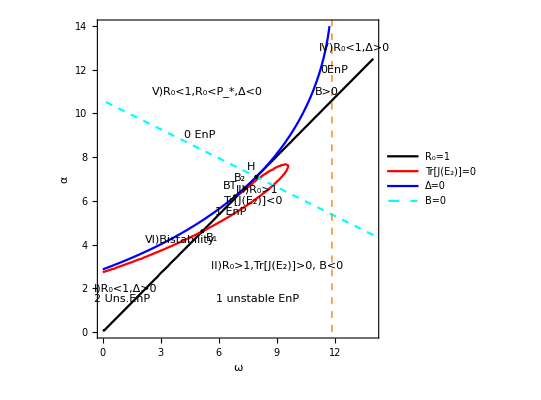

fig6n.pdf

```mathematica
(**Fig 6n of ZF*)
cn=Param
xm=0;ym=0;xM=14;yM=14;
μ/(Subscript[v, 1])//.cn//N
p1g=Graphics[{Thick,Orange,Dashed,Line[{{μ/(Subscript[v, 1])//.cn,0},{μ/(Subscript[v, 1])//.cn,45}}]}];
R0ωa=(R0//.cn/.η->α/ω);
disωa=(dis/.ceta//.cn)//FullSimplify;
Bbωa=(Bb/.ceta//.cn);

Solve[disωa==0,ω]//FullSimplify;
Solve[Bbωa==0,ω]//FullSimplify;

Print["R0-1 at BTP is "]
-1+R0ωa//.testBTP//N
Print["dis at BTP is "]
Chop[Evaluate[disωa//.testBTP//N]]
Print["Dis at H ="]
dis//.testHP//N

pR0=ContourPlot[R0ωa==1,{ω,xm,xM},{α,ym,yM},ContourStyle->Black,
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"R_0=1"}];
 
pD=ContourPlot[disωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{ Blue}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},
PlotLegends->{"Δ=0"}];

pB=ContourPlot[Bbωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{Dashed,Cyan}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"B=0"}];
trωa=((trE2//.cv1)/.ceta//.cn);

pmu=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 epi= {Black,Style[Text["V)R_0<1,R_0<P_*,Δ<0",{5.4,11}],13],Style[Text["0 EnP",{5,9}],13],
Style[Text["Tr[J(E_2)]<0",{7.8,6}],6],Style[Text["III)R_0>1",{8,6.5}],6],Style[Text["1 EnP",{6.6,5.5}],6],
Style[Text["IV)R_0<1,Δ>0",{13,13}],10],Style[Text["0EnP",{12,12}],12],
Style[Text["B>0",{11.6,11}],12],
Style[Text[" I)R_0<1,Δ>0",{1.2,2}],10],Style[Text["2 Uns.EnP",{1,1.5}],10],
Style[Text[" VI)Bistability",{4,4.2}],6],
Style[Text[" II)R_0>1,Tr[J(E_2)]>0, B<0",{9,3}],13],
Style[Text["1 unstable EnP",{8,1.5}],13]};

PH=Text["H",Offset[{-5,10},{ω,η ω}//.ParHP]];PHp={PointSize[Medium],Style[Point[{ω,η ω}//.ParHP],Yellow]};
PBT=Text["BT",Offset[{-5,10},{ω,α}//.ParBTP//N]];PBTp={PointSize[Medium],Style[Point[{ω,α}//.ParBTP//N],Red]};
BP1=Text["B_1",Offset[{10,-7},{ω,α}//.BP[[1]]]];BP1p={PointSize[Medium],Style[Point[{ω,α}//.BP[[1]]],Green]};
BP2=Text["B_2",Offset[{-5,10},{ω,α}//.BP[[2]]]];BP2p={PointSize[Medium],Style[Point[{ω,α}//.BP[[2]]],Blue]};
regions={"I",II,III,IV,V,VI};
pt=Table[{ω,α}//.test[j],{j,regions}];
pG=Table[Text[P[j],Offset[{-5,10},pt[[j]]]],{j,6}];

epiP={PH,PHp,PBT,PBTp,BP1,,BP1p,BP2,BP2p}//N;
fig6F=Show[{pR0,pmu,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6n.pdf",fig6F]
```

#### Blow-up of the Map:

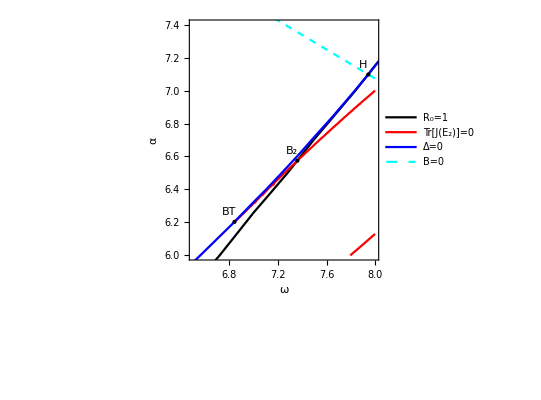

fig6ns.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=6.5;ym=6;xM=8;yM=7.4;
trωa=((trE2//.cv1)/.ceta//.cn);
pmu=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 
fig6F=Show[{pR0,pmu,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6ns.pdf",fig6F]
```

```mathematica
ωBTP=ω/.testBTP;
ωBP=ω/.testBP;
aBTP=α/.testBTP;
aBP=α/.testBP;
BR01=FindInstance[Join[{α==ω η0, ωBP<ω<ωBTP ,aBP <α<aBTP},Drop[cp,{7,9}],{η0>0}]//.Param,{ω,α},50];
Drop[BR01,30];
Print["Points betωeen BP and BTP "]
Drop[BR01,30]//N
Print["Points betωeen 0 and BP "]
BR01a=FindInstance[Join[{α==ω η0, 0<ω<ωBP ,0<α<aBP},Drop[cp,{7,9}],{η0>0}]//.Param,{ω,α},10];
BR01a
BR01a//N
Print["α and ω at BTP and boundary R0==1 are respectively "]
alBTP= ω η0//.testBTP//N
ω//.BTP//N
Print["α and ω at BP are respectively "]
alBP= ω η0//.testBP//N
ω//.BP//N

R0//.testBP//N

FindInstance[Join[{α==ω η0, (ω/.BP[[2]])<ω<(ω/.HP) ,(α/.BP[[2]]) <α<(α/.HP)},Drop[cp,{7,9}],{η0>0}]//.Param,{ω,α},3]
```

Points betωeen BP and BTP

{{ω→6.18457,α→5.52489},{ω→6.19064,α→5.5303},{ω→6.19636,α→5.53542},{ω→6.2287,α→5.5643},{ω→6.23476,α→5.56972},{ω→6.29269,α→5.62147},{ω→6.31694,α→5.64313},{ω→6.32974,α→5.65457},{ω→6.44257,α→5.75537},{ω→6.4675,α→5.77763},{ω→6.59751,α→5.89377},{ω→6.60997,α→5.90491},{ω→6.63826,α→5.93018},{ω→6.63894,α→5.93078},{ω→6.7292,α→6.01142},{ω→6.75042,α→6.03038},{ω→6.79387,α→6.06919},{ω→6.79724,α→6.0722},{ω→6.82082,α→6.09326},{ω→6.82957,α→6.10108}}

Points betωeen 0 and BP

{{ω→46/195,α→3082/14625},{ω→16/65,α→1072/4875},{ω→27/65,α→603/1625},{ω→89/39,α→5963/2925},{ω→178/65,α→11926/4875},{ω→574/195,α→38458/14625},{ω→709/195,α→47503/14625},{ω→713/195,α→47771/14625},{ω→901/195,α→60367/14625},{ω→190/39,α→2546/585}}

{{ω→0.235897,α→0.210735},{ω→0.246154,α→0.219897},{ω→0.415385,α→0.371077},{ω→2.28205,α→2.03863},{ω→2.73846,α→2.44636},{ω→2.94359,α→2.62961},{ω→3.6359,α→3.24807},{ω→3.65641,α→3.26639},{ω→4.62051,α→4.12766},{ω→4.87179,α→4.35214}}

α and ω at BTP and boundary R0==1 are respectively

6.11203

{6.84183}

α and ω at BP are respectively

4.60724

{5.15735,7.35966}

1.

{{ω→7.39223,α→6.60373},{ω→7.54757,α→6.7425},{ω→7.91456,α→7.07034}}

{α→(3 ω)/5}

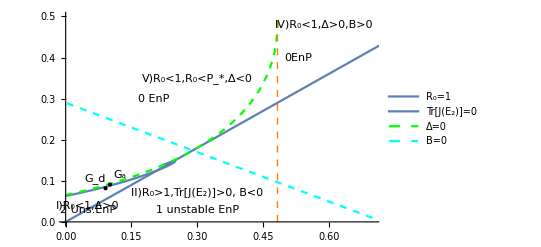

```mathematica
(**Fig Gupta*)
paramGG=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1]}->{1/2,2/10,1/10,2/10,7/100,1/10,(μ+γ+δ),(β+ μ ξ)}];
cn=paramGG;
xM=.7;La=.5;
p1g=Graphics[{Thick,Orange,Dashed,Line[{{μ/(Subscript[v, 1])//.cn,0},{μ/(Subscript[v, 1])//.cn,La}}]}];
R0ωa=(R0/.cV2//.cn/.η->α/ω);
aω=Solve[R0ωa==1,α][[1]]
pR0=Plot[α/.aω,{ω,0,20},PlotLegends->{"R_0=1"},LabelStyle->{Black,Bold}];
 disωa=(dis/.ceta//.cn);
pD=ContourPlot[disωa==0,{ω,0,xM},{α,0,La},
ContourStyle->{Thick, Dashed,Green}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},
PlotLegends->{"Δ=0"}];
Bbωa=(Bb/.ceta//.cn);
pB=ContourPlot[Bbωa==0,{ω,0,xM},{α,0,La},
ContourStyle->{Dashed,Cyan}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"B=0"}];
trωa=((trE2//.cv1)/.ceta//.cn);
pTr=ContourPlot[trωa==0,{ω,0,xM},{α,0,La},ContourStyle->Broωn,
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"},MaxRecursion->5];
epi= {Black,Style[Text["V)R_0<1,R_0<P_*,Δ<0",{0.3,0.35}],13],Style[Text["0 EnP",{0.2,0.3}],13],
Style[Text["Tr[J(E_2)]<0",{11.3,10.5}],12],Style[Text["III)R_0>1,1 EnP",{13,12}],12],
Style[Text["IV)R_0<1,Δ>0,B>0",{0.59,0.48}],10],Style[Text["0EnP",{0.53,0.4}],12],

Style[Text[" I)R_0<1,Δ>0",{0.05,0.04}],6],Style[Text["2 Uns.EnP",{0.05,0.03}],7],
Style[Text[" VI)Bistability",{3,4.7}],6],
Style[Text[" II)R_0>1,Tr[J(E_2)]>0, B<0",{0.3,0.07}],11],
Style[Text["1 unstable EnP",{0.3,0.03}],11]};
Gca1=Text["G_a",Offset[{10,10},{ω,α}//.ParGca]];GcaS1={PointSize[Medium],Style[Point[{ω,α}//.ParGca],Cyan]};
Gcd1=Text["G_d",Offset[{-10,10},{ω,α}//.ParGcd]];GcdS1={PointSize[Medium],Style[Point[{ω,α}//.ParGcd],Blue]};
epiG={Gca1,GcaS1,Gcd1,GcdS1};
mapG=Show[{pR0,pTr,pD,pB,p1g},Epilog->{epi,epiG},FrameLabel->{ω,"α"},
PlotRange->{{0,xM},{0,La}}]
```